# Introduction to SpectrumPlot

Spectrum data modelpaclet:SpectrumPlot/tutorial/Introduction to SpectrumPlot#139120837 | Working with spectrapaclet:SpectrumPlot/tutorial/Introduction to SpectrumPlot#677377107
Spectrum formattingpaclet:SpectrumPlot/tutorial/Introduction to SpectrumPlot#284766540 | Data Reductionpaclet:SpectrumPlot/tutorial/Introduction to SpectrumPlot#286520711

The function definitions in the SpectrumPlot`context provide support for importing and displaying astronomical spectral data.

This loads the package:

```mathematica
Needs["SpectrumPlot`"]
```

## Spectrum data model

Astronomical spectra are usually stored in the FITS file format, composed of a header (Import[<FITS file>,"Metadata"]) and the actual spectrum data (Import[<FITS file>,"RawData"]). The header contains all information necessary to assign the data to an astronomical observation (e.g. object name, coordinates, OBS-ID, etc.), to describe the kind of data (e.g. spectral maps, integrated intensity maps, single spectra, etc.), to specify physical units of the data content (e.g. unit of the spectral axis, velocity or frequency, unit of the data axis, e.g. Jansky, erg/s/cm^2/sr/Hz, etc.) and any other explanatory information in order to make sense of the data.

Import[file,"FITS","Metadata"] | imports header information
Import[file,"FITS","RawData"] | imports raw (unscaled) data

Manual import of spectrum data from FITS files.

Many functions from the SpectrumPlot`context work on a spectrum data object. A spectrum data object is a List of the form: List[header information, raw data]. It has to be created from the spectrum FITSpaclet:Global/ref/FITS file. If the FITSpaclet:Global/ref/FITS file contains only a single spectrum this is trivial: The FITSpaclet:Global/ref/FITS header gives all required header information, the data part gives the spectrum data.

### FITS Header

A FITSpaclet:Global/ref/FITS file is comprised of segments called Header/Data Units (HDUs), where the first HDU is called the `Primary HDU', or `Primary Array'. Any number of additional HDUs may follow the primary array. These additional HDUs are referred to as FITSpaclet:Global/ref/FITS `extensions'. 
Every HDU consists of an ASCII formatted `Header Unit' followed by an optional `Data Unit'. Each header or data unit is a multiple of 2880 bytes long. If necessary, the header or data unit is padded out to the required length with ASCII blanks or NULLs depending on the type of unit.

Each header unit contains a sequence of fixed-length 80-character keyword records which have the general form: 
KEYNAME = value / comment string

The keyword names may be up to 8 characters long and can only contain uppercase letters A to Z, the digits 0 to 9, the hyphen, and the underscore character. The keyword name is (usually) followed by an equals sign and a space character in columns 9 and 10 of the record, followed by the value of the keyword which may be either an integer, a floating point number, a complex value (i.e., a pair of numbers), a character string (enclosed in single quotes), or a Boolian value (the letter T or F). Some keywords, (e.g., COMMENT and HISTORY) are not followed by an equals sign and in that case columns 9 - 80 of the record may contain any string of ASCII text.

Each header unit begins with a series of required keywords that specify the size and format of the following data unit. A 2-dimensional image primary array header, for example, begins with the following keywords: 
SIMPLE  =                    T / file conforms to FITS standard
BITPIX  =                   16 / number of bits per data pixel
NAXIS   =                    2 / number of data axes
NAXIS1  =                  440 / length of data axis 1
NAXIS2  =                  300 / length of data axis 2

The required keywords may be followed by other optional keywords to describe various aspects of the data, such as the date and time of the observation. COMMENT or HISTORY keywords are also frequently added to further document the contents of the data file.

The last keyword in the header is always the `END' keyword which has blank value and comment fields. The header is padded with additional blank records if necessary so that it is a multiple of 2880 bytes (equivalent to 36 80-byte keywords) long. Note that the header unit may only contain ASCII text characters ranging from hexadecimal 20 to 7E); non-printing ASCII characters such as tabs, carriage-returns, or line-feeds are not allowed anywhere within the header unit.

Header information from example spectrum:

```mathematica
head=ExampleData[{"SpectrumPlot","BIMAChannelMap"}][[1]];
TableForm[head[[1;;6]]]
```

SIMPLE→{True,}
BITPIX→{-32,}
NAXIS→{4,}
NAXIS1→{32,}
NAXIS2→{32,}
NAXIS3→{256,}

```mathematica
StripHeaderComments/@head[[1;;6]]
```

{SIMPLE→True,BITPIX→-32,NAXIS→4,NAXIS1→32,NAXIS2→32,NAXIS3→256}

CleanFITSHeader[header] | strips all comments from the header entries
StripHeaderComments[header line] | removes comments from a header entry
JoinHeader[head_1,head_2,…] | join headers

Header formatting functions.

SpectrumPlot` provides functions to access and modify the header information.

GetKeyValue[head,key] | gets the value of key from the header
PutKeyValue[head,key→val] | puts key=value into the header
DeleteKey[head,key] | deletes the key from the header
FindDuplicateKeys[head_1,head_2] | finds keys that occur in head_1 and head_2
ListTFIELDS[head] | describes all TFIELDS

Access or modify header information.

Some special functions are available to identify astronomically important key values:

FindSpectralAxis[header] | which data axis corresponds to the spectral axis
FindRAAxis[header] | which data axis corresponds to the Right Ascension axis
FindDecAxis[header] | which data axis corresponds to the Declination axis

Identify astronomical dimension.

Identify which data dimension correspond to the spectral/spatial data

```mathematica
FindSpectralAxis[head]
```

3

```mathematica
FindRAAxis[head]
```

1

```mathematica
FindDecAxis[head]
```

2

### FITS Data

The primary data array can contain a 1-999 dimensional array of 1, 2 or 4 byte integers or 4 or 8 byte floating point numbers using IEEE representations. A typical primary array could contain a 1-D spectrum, a 2-D image, or a 3-D data cube.

Data from example spectrum:

```mathematica
data=ExampleData[{"SpectrumPlot","BIMAChannelMap"}][[2]];
Dimensions[data]
```

{1,1,256,32,32}

```mathematica
TableForm[head[[3;;6]]]
```

NAXIS→{4,}
NAXIS1→{32,}
NAXIS2→{32,}
NAXIS3→{256,}

Mathematica stores the data in reverse order as given by the header NAXIS keys. It also wraps the data cube in an additional List, increasing the dimension by one.

Getting rid of superfluous dimensions

```mathematica
data=flattenCube[data,head];
Dimensions[data]
```

{1,256,32,32}

The data consists of a 32×32 positions raster map. At each position a spectrum with 256 spectral channels is taken.

Accessing the data

```mathematica
data[[1,1,All,All]]//Dimensions
```

{32,32}

```mathematica
{Min@#,Max@#}&@DeleteCases[Flatten[data],Indeterminate]
```

{-36.6547,34.1493}

```mathematica
MatrixPlot[data[[1,130,All,All]],PlotRange->Automatic,PixelConstrained->True,DataReversed->True]
```

-Graphics-

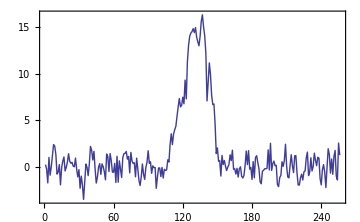

```mathematica
ListLinePlot[data[[1,All,15,15]],PlotRange->All,Frame->True,ImageSize->Medium]
```

To get a meaningful visualization of the data we need to put some physical units at the axes.

## Spectrum formatting

Some of the functions in the SpectrumPlot`context require access to the header and data information. Most of these functions are low-level functions that are not necessary for the average user. In this section we will describe how the header and data information from the FITS file are converted to a spectrum data object. Each spectrum will be stored in the form {{"Metadata"},{List of y values}}. The x-scale is calculated from the Metadata header upon display.

GetAbsoluteSpectralAxis[head] | calculate explicit values for the spectral axis

Get the absolute frequency/velocity values for each data point.

The spectral axis is given in units of m/s. The data axis is given in Jy/beam.

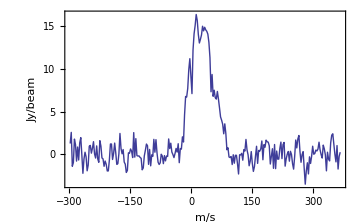

```mathematica
ListLinePlot[Transpose[{GetAbsoluteSpectralAxis[head]*10^-3,data[[1,All,15,15]]}],PlotRange->All,Frame->True,ImageSize->Medium,Axes->False,BaseStyle->{FontSize->15},FrameLabel->{"m/s","Jy/beam"}]
```

In the example data used so far, the whole data cube, i.e. the whole map, shared the same header information. This is common for regularly sampled maps, where, e.g. the absolute coordinates of an individual data point can be derived from its index and the header information. This is not necessarily always the case. For this reason we convert the data into spectrum data objects, where each spectrum is assigned its own, relevant metadata, collected from all available FITS header information.

FormatSpectrum[data,header] | converts the data into spectrum data objects
ImportSpectrum[file] | import one or more spectra

Convert/import FITS spectra.

Convert the data to the spectrum format.

```mathematica
spectra=FormatSpectrum[data,head];
```

Spectrum formating done. 1024 Spectra found in a 32 × 32 (R.A. × Dec) array.

```mathematica
Dimensions[spectra]
```

{32,32,2}

```mathematica
spectra[[15,15]]
```

{{SIMPLE→True,BITPIX→-32,NAXIS→4,NAXIS1→1,NAXIS2→1,NAXIS3→256,NAXIS4→1,EXTEND→True,BSCALE→1.,BZERO→0.,BLANK→-1,TELESCOP→NRAO 12M,CDELT1→0.005,CRPIX1→1,CRVAL1→56.7043,CTYPE1→RA---SIN,CDELT2→-0.01,CRPIX2→1,CRVAL2→68.0991,CTYPE2→DEC--SIN,CDELT3→-2600.81,CRPIX3→128.5,CRVAL3→34000.,CTYPE3→VELO-LSR,CDELT4→1.,CRPIX4→1.,CRVAL4→1.,CTYPE4→STOKES,DATE-OBS→1999-01-04T00:00:00.0,RESTFREQ→1.15271×10^11,CELLSCAL→CONSTANT,BMAJ→0.0152778,BMIN→0.0152778,OBSERVER→tth KEL,OBJECT→IC342,EPOCH→2000.,BUNIT→JY/BEAM,BPA→0.,DATAMIN→-36.6547,DATAMAX→34.1493,ORIGIN→Miriad Fits: version 1.1 27-nov-00},{0.25327,-0.244473,-1.71506,1.03068,-0.879421,0.0097036,1.18207,2.40512,2.24225,1.33502,-0.764517,-0.546583,0.253489,-1.92562,-0.0727707,0.638939,1.08128,-0.429872,-0.035979,0.523817,1.42553,0.622265,0.397134,0.503238,0.0953341,0.0179781,0.95436,-0.220185,-1.06328,-0.286032,-2.28829,-0.98148,-1.91515,-3.48687,-1.63463,0.316707,-0.0291452,-0.925608,0.337196,2.20654,1.8055,0.752775,1.67907,-0.224855,-1.72502,-1.08897,-0.0165796,0.357823,-0.797994,0.336236,0.0330825,-0.50978,-1.37767,1.39332,1.14096,-0.495349,1.43618,0.695406,-0.549897,-0.561062,0.389437,-1.66873,1.15367,-1.63294,0.661677,-0.213339,-1.1287,1.00411,1.43047,1.47356,1.66486,0.83823,1.13526,-0.631715,1.56442,0.644863,0.376567,0.459696,-1.05434,0.948371,-0.197794,-1.43176,-1.99165,-1.05955,0.325173,-0.797091,-1.33285,-0.0542229,0.518403,1.7459,0.393945,0.55625,-0.681775,0.123913,-0.0717658,-0.0439017,-2.29421,-1.09347,-0.107982,-0.105677,-1.03387,-0.046841,-1.18831,-0.250906,-0.368276,-0.310492,0.769749,0.538752,2.43631,3.56858,2.40484,3.5327,3.99676,4.38099,5.45252,6.47564,7.35641,6.46419,6.62432,7.4997,6.79189,9.3373,7.31569,11.3048,13.0852,14.0577,14.389,14.5563,14.86,14.4369,14.979,13.963,13.4535,13.0197,14.0374,15.647,16.3528,15.0586,14.0929,12.1952,7.10239,9.11448,11.187,9.91873,7.70704,6.7053,6.76993,4.61979,1.44372,2.04915,0.609943,0.683794,-0.972196,1.24542,0.266655,0.693843,0.0970313,-0.37799,-0.0163991,0.271731,1.30639,0.679949,1.80415,-0.247162,-0.188215,-0.761393,-0.14242,-1.08401,-0.197549,0.0135975,-0.993207,-1.1817,-0.912727,0.153965,1.71886,0.251242,1.75624,-0.233538,-0.0557876,-1.33939,0.578441,-1.16679,1.01366,1.20657,0.479215,-0.174132,-1.58612,-1.80484,-0.458567,-0.36082,-0.178281,-0.194348,-0.141621,1.83792,-0.322953,2.54433,-0.37536,0.367283,0.632668,0.132611,0.183506,-1.88134,-2.11309,-1.14829,-0.892687,0.563191,0.0684625,0.684481,2.44518,0.0772046,-1.08187,-1.16946,0.204559,1.32042,0.107878,-0.598194,1.20869,1.21482,-0.661142,-1.93288,-1.93952,-1.15952,-0.776684,-1.39569,-0.524046,-0.422682,0.975314,1.60071,-0.925701,-0.530241,0.991526,-0.430284,0.045887,1.48438,0.721144,0.141807,1.04822,0.95333,-1.25845,-1.92157,-0.284268,0.251807,-0.553212,-2.21509,-0.0738008,1.95772,1.34513,-0.65906,0.859924,-0.787554,1.1443,1.78666,-0.961647,-1.39028,2.57114,1.26939}}

MetaDataQ[list] | test for a list of rules
MetaDataPattern | pattern matching the metadata
SpectrumQ[spec] | True if spec is a spectrum data object
SpectrumPattern | pattern matching a spectrum data object
MultipleSpectraQ[list] | True if list is a list of spectrum data objects
SpectrumArrayQ[array] | True if array is an array of spectrum data objects

Testing for spectrum data objects.

Testing the data structure:

```mathematica
MetaDataQ[head]
```

True

```mathematica
MetaDataQ[spectra[[15,15,1]]]
```

True

```mathematica
SpectrumQ[spectra[[15,15]]]
```

True

```mathematica
SpectrumArrayQ[spectra]
```

True

```mathematica
MultipleSpectraQ[spectra]
```

False

## Working with spectra

Plotting spectra

The SpectrumPlot`context offers the function SpectrumPlot to plot one or more astronomical spectra. By default the bottom x-axis is given in velocity units (usually in km/s) the top x-axis in frequency units (usually in GHz).

Plotting an example spectrum:

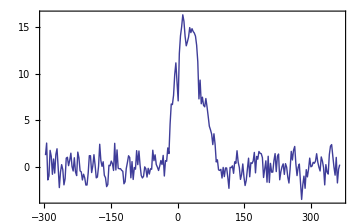

```mathematica
SpectrumPlot[spectra[[15,15]],ImageSize->Medium]
```

"FrequencyAxis" | Top | Shows the frequency at the 2nd x-axis. Switch off with None.
"VelocityUnits" | "km/s" | Unit of the velocity axis. 
"RestFrequency" | Automatic | Take the rest frequency f_0 from the header to calculate the velocity v=c (1-f/f_0)

Options for SpectrumPlot..

You can also plot multiple spectra in the same plot.

Give a list of spectra as argument:

```mathematica
SpectrumPlot[Flatten[spectra[[14;;17,14;;17]],1],ImageSize->Medium]
```

-Graphics-

SpectrumPlot takes all standard Options of ListPlotpaclet:ref/ListPlot.

Change plotting options:

```mathematica
SpectrumPlot[Flatten[spectra[[14;;17,14;;17]],1],ImageSize->Medium,
PlotRange->{-2,40},InterpolationOrder->1,FrameStyle->{{Black,Black},{Black,Red}},
Epilog->{Dashed,Gray,Line[{{25,-10},{25,100}}]}]
```

-Graphics-

### Extracting spectrum data and properties

The spectrum data can be easily extracted from the spectrum data object.

Part[spec,2] | directly access raw spec data
ComposeXYSpectrum[spec] | calculate {{x_1,y_1},…} spectrum data
SpectralAxisType[head] | determine type of spectral dimension
SpectralAxisConfiguration[spec] | retrieve full information on spectral dimension
GetCoordinateSystem[spec] | determine kind of coordinate system/map projection
GetObservedCoordinates[spec] | determine coordinates of observation

XXXX.

Extract raw data:

```mathematica
Part[spectra[[15,15]],2]//Short
```

{0.25327,-0.244473,«253»,1.26939}

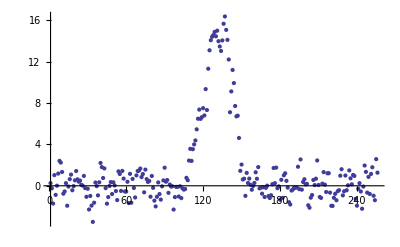

```mathematica
ListPlot[%,PlotRange->All]
```

To retrieve a related x-values we can use the function ComposeXY

Extract {x,y} data pairs:

```mathematica
ComposeXYSpectrum[spectra[[15,15]]]//Short
```

{{365604.,0.25327},«254»,{-297604.,«19»}}

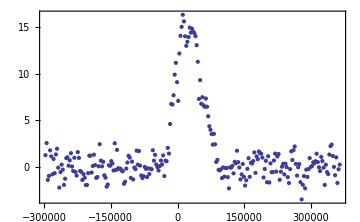

```mathematica
ListPlot[%,PlotRange->All,Axes->False,Frame->True,ImageSize->Medium]
```

The X-values are calculated from the header information and are in units as specified in the header. In this case the header information says VELO-LSR, i.e. velocity in SI units in the local standard of rest frame.

Determine the type of the spectral dimension:

```mathematica
SpectralAxisType[head]
```

VELO-LSR

Determine the full configuration of the spectral dimension:

```mathematica
SpectralAxisConfiguration[spectra[[15,15]]]
```

{VELO-LSR,128.5,-2600.81,34000.,256}

Astronomical data comes in many subtle variations in terms of the used coordinate system, applied map prjections, and so on. To query where the data has been actually observed SpectrumPlot offers functions to extract the related information from the header.

Determine the type of the coordinate system:

```mathematica
GetCoordinateSystem[spectra[[15,15]]]
```

{RA---SIN,DEC--SIN}

Determine the absolute coordinate (in Degrees) of an observed spectrum:

```mathematica
GetObservedCoordinates[spectra[[15,15]]]
```

{56.7177,68.0891}

Determine the relative coordinate offset (in Arcseconds) of an observed spectrum:

```mathematica
GetObservedCoordinates[spectra[[15,15]],Method->"RelativeCoordinates"]*3600
```

{18.,-36.}

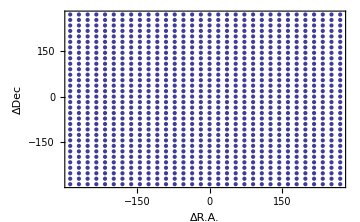

```mathematica
ListPlot[3600*GetObservedCoordinates[#,Method->"RelativeCoordinates"]&/@Flatten[spectra,1],Frame->True,Axes->False,ImageSize->Medium,FrameLabel->{"ΔR.A.","ΔDec"}]
```

## Data Reduction

SpectrumPlot offers several functions to perform standard data reduction task, including smoothing, averaging, masking and fitting.

AverageSpectrum[{s_1,s_2,…}] | average a list of spectra s_i
CalculateRMS[spec] | calculate the RMS of spec
MaskSpectrum[spec,{{v_min,v_max},…},f_0] | masks parts of the spectrum to be ignored during the fitting
RegridSpectralAxis[spec_r,spec] | spectral regridding of spec to the reference spectrum spec_r
SmoothSpectrum[spec] | smoothes a spectrum spec
SubtractBaseline[spec] | subtracts a polynomial baseline from a spectrum spec

Data redutction functions.

If a list of spectra have a common spectral axis AverageSpectrum can be used to average them. So far two methods are supported: simple arithmetic mean and RMS weighted mean.

Average spectrum of a 2 spectra:

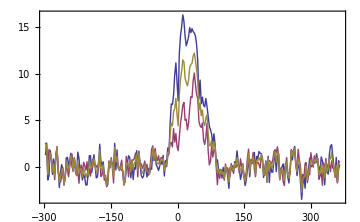

```mathematica
SpectrumPlot[{spectra[[15,15]],spectra[[14,14]],AverageSpectrum[{spectra[[15,15]],spectra[[14,14]]}]/.Missing[]->0},ImageSize->Medium,PlotStyle->{Automatic,Automatic,Thick}]
```

Average spectrum of a whole map:

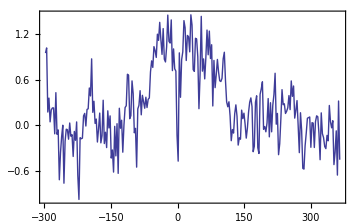

```mathematica
SpectrumPlot[AverageSpectrum[Flatten[spectra,1]]/.Missing[]->0,ImageSize->Medium]
```

Averaging is also possible using RMS weighting, if the header information contains information on the RMS. This is usually only the case after baseline removal.

Calculate the RMS of a spectrum:

```mathematica
CalculateRMS[spectra[[15,15]]]
```

4.2915

```mathematica
CalculateRMS[spectra[[4,4]]]
```

1.90767

```mathematica
SpectrumPlot[spectra[[15,15]],ImageSize->Medium]
-Graphics-
```

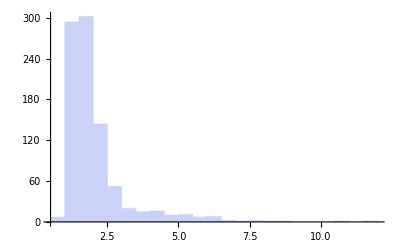

```mathematica
Histogram[CalculateRMS/@Flatten[spectra,1]]
```

It appears strange that the RMS seems to vary across the map. The reason for this is, that CalculateRMSpaclet:SpectrumPlot/ref/CalculateRMS calculates the RMS acoss the whole band, i.e. including the line signal! We have to blank out (mask) the signal, to calculate just the RMS of the noise.

Calculate the RMS of a spectrum with the line masked:

```mathematica
CalculateRMS[MaskSpectrum[spectra[[15,15]],{-40,120}]/.Missing[]->0]
```

0.97062

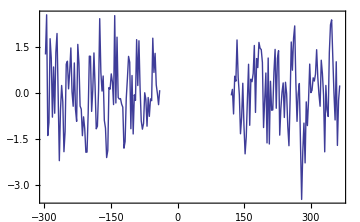

```mathematica
SpectrumPlot[MaskSpectrum[spectra[[15,15]],{-40,120}],ImageSize->Medium]
```

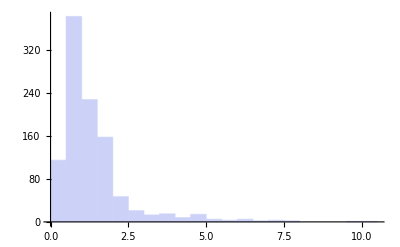

```mathematica
Histogram[CalculateRMS[MaskSpectrum[#,{-40,120}]/.Missing[]->0]&/@Flatten[spectra,1]]
```